# Knot for Sail aka Boats Mah Goats

```mathematica
ClearAll[f]
```

7.0473

1168.3

{0,4.3}

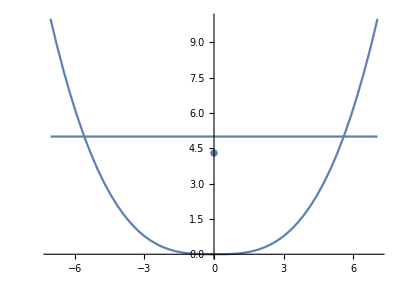

```mathematica
BoatCurve = 1/7 x^2+1/4 Sin[Abs[1*x]];
BoatCurve = Abs[x^3/35];

BoatDensity = .03; (*g/ml*)
MassBalast = 1000 ;  (*g*)
COBallast = {0,1};

MastMass = 96; (*g*)
MastCom = {0, 27.34};

BoatLength = 40;
BoatWidth = 17;
BoatHeight = 10;

xbd = x/.FindRoot[BoatHeight-BoatCurve, {x, 10}]

boat = ImplicitRegion[BoatCurve<y<BoatHeight,{{x,-xbd,xbd},{y,-2,BoatHeight}}];
water = ImplicitRegion[y<d,{{x,-xbd,xbd},{y,-2,BoatHeight}}];
under = RegionIntersection[boat,water];

totalMass = 1168.3(*N[BoatLength*Integrate[BoatDensity,{x,y}∈boat]+MassBalast+MastMass]*)
mass = N[BoatLength*Integrate[BoatDensity,{x,y}∈boat]];
disp = BoatLength*Integrate[.997,{x,y}∈under];

com = {0,4.3}(*1/totalMass*(RegionCentroid[boat]*mass+MassBalast*COBallast+MastMass*MastCom)*)

Show[Plot[BoatCurve, {x,-xbd,xbd}, PlotRange->{{-xbd,xbd},{0,BoatHeight}}, AspectRatio->Automatic],Plot[Tan[HeelAngle Degree]*(x)+5, {x, -xbd,xbd}], ListPlot[{{com[[1]],com[[2]]}}]]

(*Show[RegionPlot[{water/.{d->5}, boat, under/.{d->5}}, AspectRatio->Automatic], ListPlot[{com}]]*)

com = Append[com, 0];
```

```mathematica
Torque[theta_]:=Module[{},
boat = ImplicitRegion[BoatCurve<y<BoatHeight,{{x,-xbd,xbd},{y,-2,BoatHeight}}];
water = ImplicitRegion[If[theta<90,y<Tan[theta Degree]*x+d,y>Tan[theta Degree]*x+d],{{x,-xbd,xbd},{y,-2,BoatHeight}}];

under = RegionIntersection[boat,water];
disp = .997*BoatLength*Area[under];
draft = N[d/.FindRoot[disp==totalMass,{d,-30,30},AccuracyGoal->3][[1]], 3];
cob = Append[RegionCentroid[under/.{d->draft}],0];
buoyancy = totalMass*98/10*{-Sin[theta Degree],Cos[theta Degree],0};
torque = Cross[cob-com,buoyancy][[3]];
torque
]
```

2.02635×10^-12

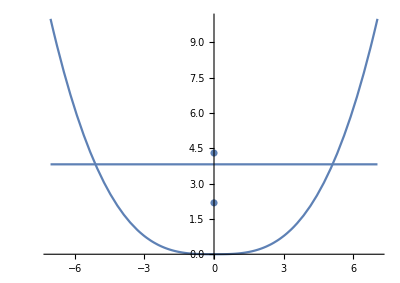

```mathematica
HeelAngle = 0;
Torque[HeelAngle]

Show[Plot[BoatCurve, {x,-xbd,xbd}, PlotRange->{{-xbd,xbd},{0,BoatHeight}}, AspectRatio->Automatic],Plot[Tan[HeelAngle Degree]*(x)+draft, {x, -xbd,xbd}], ListPlot[{{com[[1]],com[[2]]},{cob[[1]],cob[[2]]}}]]
```

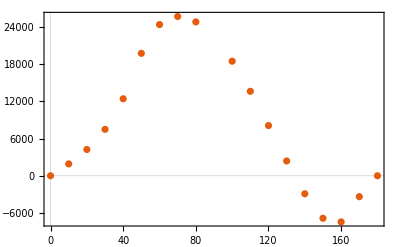

```mathematica
ListPlot[Table[{theta,Torque[theta]},{theta,{0,10,20,30,40,50,60,70,80,100,110,120,130,140,150,160,170,180}}], PlotTheme->"Scientific"]
```

```mathematica
com = 1/(mass+MastMass)*(RegionCentroid[boat]*mass+MastMass*MastCom)
mass+MastMass
```

{4.14402×10^-17,14.4114}

238.708